```mathematica
(* This notebook is used to run the manipulates to toy with adjusting parameters and view simple visualizatoins. The model and data i/o live in the model.wl file *)
```

National Model-- Used to determine best - guess model parameters

```mathematica
Manipulate[
Module[{distance,t},
params=countryParams[country,pC,pH,medianHospitalizationAge,ageCriticalDependence,ageHospitalizedDependence];
thisCountryData=countryData[country];
icuCapacity=2*params["ventalators"]/params["Population"];

distance[t_]:=Piecewise[countryHistoricalDistancing[country,t]]; 

{sol,evts}=CovidModel[
r0natural,
daysUntilNotInfectiousOrHospitalized,
daysFromInfectedToInfectious,
daysUntilNotInfectiousOrHospitalized,
daysToLeaveHosptialNonCritical,
pPCRNH,
pPCRH,
daysTogoToCriticalCare,
daysFromCriticalToRecoveredOrDeceased,
fractionOfCriticalDeceased,
params["importtime0"],
importlength0,
initialInfectionImpulse,
tmax,
1-pH-pC,
pH,
pC,
containmentThresholdRatio0,
icuCapacity,
distance
];


(* redefine this with p, for dynamic setting *)
events=Association[Flatten[evts]];

(* make plots *)
setDistancingPlot=Plot[distance[t],{t,0,300},PlotRange->{0,1},
Frame->{True,True,False,True},
FrameTicks->{{{{0,"100%"},{0.2,"80%"},{0.4,"60%"},{0.6,"40%"},{0.8,"20%"},{1,"0%"}},{{0,0},{0.2,0.2*r0natural0},{0.4,0.4*r0natural0},{0.6,0.6*r0natural0},{0.8,0.8*r0natural0},{1,r0natural0}}},{dateticks, None}},
FrameLabel->{{"Social Distance (%)","R0"},{None,None}},
ImageSize->475];
deathsPlot=LogPlot[Evaluate[params["Population"]*Deaq[t]/.sol],
{t,40,300},
PlotRange->{1,0.1*params["Population"]},
Frame->{True,True,False,False},
FrameTicks->{{Automatic,None},{dateticks, None}},
ImageSize->475,
PlotLabel->Style["Deaths (cumulative)",FontSize->18],
Epilog->{Point@({#["day"],Log[#["death"]]}&/@Select[thisCountryData,(#["death"] > 0)&])}];
progressionPlot=LogPlot[{
Evaluate[params["Population"]*(Eq[t])/.sol],
Evaluate[params["Population"]*(PCR[t])/.sol],
Evaluate[params["Population"]*(Iq[t])/.sol],
params["Population"],
},{t,40,300},Epilog->{Point@({#["day"],Log[#["positive"]]}&/@thisCountryData)},  PlotRange->{1,3*params["Population"]},
Frame->{True,True,False,False},
PlotLabel->Style["Case Progression",FontSize->18],
FrameTicks->{{Automatic,None},{dateticks, None}},
PlotLegends->SwatchLegend[{"Infected","PCR Confirmed (cumulative)","Infectious", "Population"}],
ImageSize->475];
criticalPlot=Plot[{Evaluate[params["Population"]*CCq[t]/.sol],2*params["ventalators"]},
{t,40,300},
PlotRange->{1,params["Population"]/500},
Frame->{True,True,False,False},
FrameTicks->{{Automatic,None},{dateticks, None}},
ImageSize->475,
PlotLabel->Style["Need Critical Care",FontSize->18],
Filling->{2->{{1},{LightRed,White}}},
PlotLegends->SwatchLegend[{"Critical Care Needed","ICU capacity (ventalator constrained)"}]];
ageDependencyPlot=Plot[{infectedCritical[a,medianHospitalizationAge, pC,ageCriticalDependence],infectedHospitalized[a, medianHospitalizationAge, pH,ageHospitalizedDependence],noCare[a, medianHospitalizationAge, pC,pH,ageCriticalDependence,ageHospitalizedDependence ]}, {a,0,100},
Frame->{True,True,False,False},
PlotLabel->Style["Case severity ratios by age",FontSize->Automatic],
PlotLegends->SwatchLegend[{"Critical","Hospitalized","Home Care"}],
ImageSize->200,
FrameLabel->{{"Fraction (%)",None},{"Age (years)",None}}
];

summary=Column[{Style["Result summary:",Bold], Grid[KeyValueMap[Flatten[{##}]&]@<|"Deaths"->If[KeyExistsQ[events, "containment"],params["Population"]*Deaq[t]/.sol/.{t->events["containment"][[1]][[1]]}, params["Population"]*Deaq[t]/.sol/.{t->1000}] ,"PCR Confirmed"->If[KeyExistsQ[events, "containment"],params["Population"]*PCR[t]/.sol/.{t->events["containment"][[1]][[1]]}, params["Population"]*PCR[t]/.sol/.{t->1000}],
"Population Infected"->If[KeyExistsQ[events, "containment"],PercentForm[PCR[t]/.sol/.{t->events["containment"][[1]][[1]]}],PercentForm[ PCR[t]/.sol/.{t->1000}]],
"Fatality Rate"->If[KeyExistsQ[events, "containment"],PercentForm[(Deaq[t]/PCR[t])/.sol/.{t->events["containment"][[1]][[1]]}], PercentForm[(Deaq[t]/PCR[t])/.sol/.{t->1000}]],
"Date Contained"->If[KeyExistsQ[events, "containment"],DateString[DatePlus[{2020,1,1},events["containment"][[1]][[1]]-1]], "Not Contained"]|>, 
Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text"]}];

Grid[{
{
setDistancingPlot,
Column[{
Style["Demographic parameters:",Bold], Grid[KeyValueMap[Flatten[{##}]&]@(<|"Population"->#["Population"], "Import Time"->DateString[DatePlus[{2020,1,1},#["importtime0"]-1]],"Ventalators"->#["ventalators"],"Probability No Care Needed"->PercentForm[#["pS"]],"Probability ICU"->PercentForm[#["pC"]],"Probability Hospitalized (not ICU)"->PercentForm[#["pH"]]|>&)@params, Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text"],
Row[{
ageDependencyPlot
}]
}]
},
{Column[{
Style["Model Outputs:",Bold],
If[KeyExistsQ[events, "containment"],containedGraphics,heardGraphics],
If[KeyExistsQ[events, "icu"]&&(!KeyExistsQ[events, "containment"]||(events["icu"][[1]][[1]]-events["containment"][[1]][[1]])<=0),icuOvershotTextGraphics,icuBelowCapacityGraphics]
}]},
{
Show[deathsPlot,If[KeyExistsQ[events, "containment"],Graphics[{LightGray,Rectangle[{events["containment"][[1]][[1]],Log[1]},{300,Log[0.1*params["Population"]]}]}],Graphics[]]],
Show[progressionPlot,If[KeyExistsQ[events, "containment"],Graphics[{LightGray,Rectangle[{events["containment"][[1]][[1]],Log[1]},{300,Log[params["Population"]]}]}],Graphics[]]]
},
{
Show[criticalPlot,If[KeyExistsQ[events, "containment"],Graphics[{LightGray,Rectangle[{events["containment"][[1]][[1]],1},{300,params["Population"]/500}]}],Graphics[]]],
summary,
}
}]
],{country,countries},{{initialInfectionImpulse,initialInfectionImpulse0},1,100},{{r0natural,r0natural0},2.5,5},{{daysFromInfectedToInfectious,daysFromInfectedToInfectious0},1,10},{{daysUntilNotInfectiousOrHospitalized,daysUntilNotInfectiousOrHospitalized0},1,10},{{daysFromCriticalToRecoveredOrDeceased,daysFromCriticalToRecoveredOrDeceased0},1,20},{{fractionOfCriticalDeceased,fractionOfCriticalDeceased0},0,1},
{{medianHospitalizationAge,medianHospitalizationAge0},0,100},{{ageCriticalDependence,ageCriticalDependence0},0,100},{{ageHospitalizedDependence,ageHospitalizedDependence0},0,100},{{pH,pH0},0,0.5},{{pC,pC0},0,0.5},
{{daysToLeaveHosptialNonCritical,daysToLeaveHosptialNonCritical0},0,10},
{{pPCRNH,pPCRNH0},0,1},
{{pPCRH,pPCRH0},0,1},
{{daysTogoToCriticalCare,daysTogoToCriticalCare0},0,10}
]
```

Now we are going to look at the outbreak state-by-state. This setup fetches state-level COVID data from covidtracking.com, and age distribution data from Mathematica’s datasets. Age buckets are not totally even, but we can just go down to the smallest applicable eg 3 -> 0, 90 -> 85 etc. (warning: Because of data fetching it’s somewhat slow)

```mathematica
Manipulate[
Module[{distance,t},
params=stateParams[state,pC0,pH0,medianHospitalizationAge0,ageCriticalDependence0,ageHospitalizedDependence0];
thisStateData=Select[parsedData,(#["state"]==state&&#["positive"]>0)&];
icuCapacity=params["icuBeds"]/params["Population"];
hospitalCapacity=(1-params["bedUtilization"])*params["staffedBeds"]/params["Population"];
hospitalizationData=stateHospitalizationData[state];

distance[t_]:=Piecewise[stateHistoricalDistancing[state,scenario,t],1];
{sol,evts}=CovidModel[
r0natural0,
daysUntilNotInfectiousOrHospitalized0,
daysFromInfectedToInfectious0,
daysUntilNotInfectiousOrHospitalized0,
daysToLeaveHosptialNonCritical0,
pPCRNH0,
pPCRH0,
daysTogoToCriticalCare0,
daysFromCriticalToRecoveredOrDeceased0,
fractionOfCriticalDeceased0,
params["importtime0"],
importlength0,
initialInfectionImpulse0,
tmax,
params["pS"],
params["pH"],
params["pC"],
containmentThresholdRatio0,
icuCapacity,
distance,
hospitalCapacity
];

events=Association[Flatten[evts]];

baseline=distance[1];
(* make plots *)
setDistancingPlot=Plot[distance[t]/baseline,{t,0,300},PlotRange->{0,1},
Frame->{True,True,False,True},
FrameTicks->{{{{0,"100%"},{0.2,"80%"},{0.4,"60%"},{0.6,"40%"},{0.8,"20%"},{1,"0%"}},{{0,0},{0.2,0.2*r0natural0*baseline},{0.4,0.4*r0natural0*baseline},{0.6,0.6*r0natural0*baseline},{0.8,0.8*r0natural0*baseline},{1,r0natural0*baseline}}},{dateticks, None}},
FrameLabel->{{"Social Distance (%)","R0"},{None,None}},
ImageSize->475,
PlotStyle->Thick,AxesStyle->Thick,FrameTicksStyle->Directive[Black,15],
Epilog->{Directive[Gray,Thick,Dashed],Line[{{today,0},{today,1}}],Directive[Gray],Text["Today",{today+20,0.8}]}
];
deathsPlot=LogPlot[Evaluate[params["Population"]*Deaq[t]/.sol],
{t,0,300},
PlotRange->{1,0.1*params["Population"]},
Frame->{True,True,False,False},
FrameTicks->{{Automatic,None},{dateticks, None}},
ImageSize->475,
PlotStyle->Thick,AxesStyle->Thick,FrameTicksStyle->Directive[Black,15],
Epilog->{Point@({#["day"],Log[#["death"]]}&/@Select[thisStateData,(#["death"] > 0)&]),Directive[Gray,Thick,Dashed],Line[{{today,0},{today,0.1*params["Population"]}}],Directive[Gray],Text["Today",{today+20,0.8*Log[0.1*params["Population"]]}]}];
progressionPlot=LogPlot[{
Evaluate[params["Population"]*(Eq[t])/.sol],
Evaluate[params["Population"]*(PCR[t])/.sol],
Evaluate[params["Population"]*(Iq[t])/.sol],
params["Population"]
},{t,0,300},Epilog->{Point@({#["day"],Log[#["positive"]]}&/@thisStateData),Directive[Gray,Thick,Dashed],Line[{{today,Log[1]},{today,Log[params["Population"]]}}],Directive[Gray],Text["Today",{today+15,0.8*Log[params["Population"]]}]},  PlotRange->{1,params["Population"]},
Frame->{True,True,False,False},
PlotStyle->Thick,
FrameTicks->{{Automatic,None},{dateticks, None}},
FrameTicksStyle->Directive[Black,15],
PlotLegends->Placed[SwatchLegend[{"Infected","PCR Confirmed (cumulative)","Infectious", "Population"}],{{0.7,0.8},{0.5,1}}],
ImageSize->475];
criticalPlot=Plot[{Evaluate[params["Population"]*CCq[t]/.sol],params["icuBeds"]},
{t,0,300},
PlotRange->{1,params["Population"]/500},
Frame->{True,True,False,False},
FrameTicks->{{Automatic,None},{dateticks, None}},
ImageSize->475,
PlotStyle->Thick,
Epilog->{Directive[Gray,Thick,Dashed],Line[{{today,1},{today,params["Population"]/500}}],Directive[Gray],Text["Today",{today+20,0.8*params["Population"]/500}]},
FrameTicksStyle->Directive[Black,15],
Filling->{2->{{1},{LightRed,White}}},
PlotLegends->Placed[SwatchLegend[{"Critical Care Needed","ICU capacity"}],{{0.7,1},{0.5,1}}]];
hospitalPlot=Plot[{Evaluate[params["Population"]*HHq[t]/.sol],params["Population"]*hospitalCapacity},
{t,0,300},
PlotRange->{1,params["Population"]/300},
Frame->{True,True,False,False},
FrameTicks->{{Automatic,None},{dateticks, None}},
ImageSize->475,
PlotStyle->Thick,
Epilog->{Point@({#["day"],#["hospitalizations"]}&/@hospitalizationData),Directive[Gray,Thick,Dashed],Line[{{today,1},{today,params["Population"]/300}}],Directive[Gray],Text["Today",{today+20,0.8*params["Population"]/300}]},
FrameTicksStyle->Directive[Black,15],
Filling->{2->{{1},{LightRed,White}}},
PlotLegends->Placed[SwatchLegend[{"Hosptial Care Needed","Hospital system capacity"}],{{0.7,1},{0.5,1}}]];

summary=Column[{Style["Result summary:",Bold], Grid[KeyValueMap[Flatten[{##}]&]@<|"Deaths"->If[KeyExistsQ[events, "containment"],params["Population"]*Deaq[t]/.sol/.{t->events["containment"][[1]][[1]]}, params["Population"]*Deaq[t]/.sol/.{t->1000}] ,"PCR Confirmed"->If[KeyExistsQ[events, "containment"],params["Population"]*PCR[t]/.sol/.{t->events["containment"][[1]][[1]]}, params["Population"]*PCR[t]/.sol/.{t->1000}],
"Population Infected"->If[KeyExistsQ[events, "containment"],(RSq[t]+RHq[t]+RCq[t])/.sol/.{t->events["containment"][[1]][[1]]},(RSq[t]+RHq[t]+RCq[t])/.sol/.{t->1000}],
"Fatality Rate"->If[KeyExistsQ[events, "containment"],(Deaq[t]/(RSq[t]+RHq[t]+RCq[t]))/.sol/.{t->events["containment"][[1]][[1]]}, (Deaq[t]/(RSq[t]+RHq[t]+RCq[t]))/.sol/.{t->1000}],
"Fatality Rate (PCR)"->If[KeyExistsQ[events, "containment"],(Deaq[t]/PCR[t])/.sol/.{t->events["containment"][[1]][[1]]}, (Deaq[t]/PCR[t])/.sol/.{t->1000}],
"Date Contained"->If[KeyExistsQ[events, "containment"],DateString[DatePlus[{2020,1,1},events["containment"][[1]][[1]]-1]], "Not Contained"],
"Date ICU Over Capacity"->If[KeyExistsQ[events, "icu"]&&(!KeyExistsQ[events, "containment"]||(events["icu"][[1]][[1]]-events["containment"][[1]][[1]])<=0),DateString[DatePlus[{2020,1,1},events["icu"][[1]][[1]]-1]],"ICU Under capacity"],
"Date Hospitals Over Capacity"->If[KeyExistsQ[events, "hospital"]&&(!KeyExistsQ[events, "containment"]||(events["hospital"][[1]][[1]]-events["containment"][[1]][[1]])<=0),DateString[DatePlus[{2020,1,1},events["hospital"][[1]][[1]]-1]],"Hospitals Under capacity"]|>, 
Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text"]}];


(* organize plots and output *)
Grid[{
{
setDistancingPlot,Column[{Style["Demographic parameters:",Bold], Grid[KeyValueMap[Flatten[{##}]&]@(<|"Population"->#["Population"], "Import Time"->DateString[DatePlus[{2020,1,1},#["importtime0"]-1]],"R0"->#["R0"],"Ventalators"->#["ventalators"],"Probability No Care Needed"->PercentForm[#["pS"]],"Probability ICU"->PercentForm[#["pC"]],"Probability Hospitalized (not ICU)"->PercentForm[#["pH"]]|>&)@params, Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text"]}],
},
{Column[{
Style["Model Outputs:",Bold],
If[KeyExistsQ[events, "containment"],containedGraphics,heardGraphics],
If[KeyExistsQ[events, "icu"]&&(!KeyExistsQ[events, "containment"]||(events["icu"][[1]][[1]]-events["containment"][[1]][[1]])<=0),icuOvershotTextGraphics,icuBelowCapacityGraphics]
}]},
{
Show[deathsPlot,If[KeyExistsQ[events, "containment"],Graphics[{LightGray,Rectangle[{events["containment"][[1]][[1]],Log[1]},{300,Log[0.1*params["Population"]]}]}],Graphics[]]],
Show[progressionPlot,If[KeyExistsQ[events, "containment"],Graphics[{LightGray,Rectangle[{events["containment"][[1]][[1]],Log[1]},{300,Log[params["Population"]]}]}],Graphics[]]]
},
{
Show[criticalPlot,If[KeyExistsQ[events, "containment"],Graphics[{LightGray,Rectangle[{events["containment"][[1]][[1]],1},{300,params["Population"]/500}]}],Graphics[]]],
Show[hospitalPlot, If[KeyExistsQ[events, "containment"],Graphics[{LightGray,Rectangle[{events["containment"][[1]][[1]],1},{300,params["Population"]/500}]}],Graphics[]]]
},
{
summary
}}]]
,{state,distancingStates},{scenario,{"scenario1","scenario2","scenario3","scenario4"}}]
```

```mathematica
(* to deprecate since we are going to create the plot images on the frontend *)
```

```mathematica
statePlots[state_,scenario_]:=Module[{distance,t},
params=stateParams[state,pC0,pH0,medianHospitalizationAge0,ageCriticalDependence0,ageHospitalizedDependence0];
thisStateData=Select[parsedData,(#["state"]==state&&#["positive"]>0)&];
icuCapacity=params["icuBeds"]/params["Population"];
hospitalCapacity=(1-params["bedUtilization"])*params["staffedBeds"]/params["Population"];

distance[t_]:=Piecewise[stateHistoricalDistancing[state,scenario,t],1];

{sol,evts}=CovidModel[
r0natural0,
daysUntilNotInfectiousOrHospitalized0,
daysFromInfectedToInfectious0,
daysUntilNotInfectiousOrHospitalized0,
daysToLeaveHosptialNonCritical0,
pPCRNH0,
pPCRH0,
daysTogoToCriticalCare0,
daysFromCriticalToRecoveredOrDeceased0,
fractionOfCriticalDeceased0,
params["importtime0"],
importlength0,
initialInfectionImpulse0,
tmax,
params["pS"],
params["pH"],
params["pC"],
containmentThresholdRatio0,
icuCapacity,
distance,
hospitalCapacity
];

events=Association[Flatten[evts]];

baseline=distance[1];
(* make plots *)
setDistancingPlot=Plot[distance[t]/baseline,{t,0,300},PlotRange->{0,1},
Frame->{True,True,False,True},
FrameTicks->{{{{0,"100%"},{0.2,"80%"},{0.4,"60%"},{0.6,"40%"},{0.8,"20%"},{1,"0%"}},{{0,0},{0.2,0.2*r0natural0*baseline},{0.4,0.4*r0natural0*baseline},{0.6,0.6*r0natural0*baseline},{0.8,0.8*r0natural0*baseline},{1,r0natural0*baseline}}},{dateticks, None}},
FrameLabel->{{"Social Distance (%)","R0"},{None,None}},
ImageSize->475,
PlotStyle->Thick,AxesStyle->Thick,FrameTicksStyle->Directive[Black,15],
Epilog->{Directive[Gray,Thick,Dashed],Line[{{today,0},{today,1}}],Directive[Gray],Text["Today",{today+20,0.8}]}
];
deathsPlot=LogPlot[Evaluate[params["Population"]*Deaq[t]/.sol],
{t,0,300},
PlotRange->{1,0.1*params["Population"]},
Frame->{True,True,False,False},
FrameTicks->{{Automatic,None},{dateticks, None}},
ImageSize->475,
PlotStyle->Thick,AxesStyle->Thick,FrameTicksStyle->Directive[Black,15],
Epilog->{Point@({#["day"],Log[#["death"]]}&/@Select[thisStateData,(#["death"] > 0)&]),Directive[Gray,Thick,Dashed],Line[{{today,0},{today,0.1*params["Population"]}}],Directive[Gray],Text["Today",{today+20,0.8*Log[0.1*params["Population"]]}]}];
progressionPlot=LogPlot[{
Evaluate[params["Population"]*(Eq[t])/.sol],
Evaluate[params["Population"]*(PCR[t])/.sol],
Evaluate[params["Population"]*(Iq[t])/.sol],
params["Population"]
},{t,0,300},Epilog->{Point@({#["day"],Log[#["positive"]]}&/@thisStateData),Directive[Gray,Thick,Dashed],Line[{{today,Log[1]},{today,Log[params["Population"]]}}],Directive[Gray],Text["Today",{today+15,0.8*Log[params["Population"]]}]},  PlotRange->{1,params["Population"]},
Frame->{True,True,False,False},
PlotStyle->Thick,
FrameTicks->{{Automatic,None},{dateticks, None}},
FrameTicksStyle->Directive[Black,15],
PlotLegends->Placed[SwatchLegend[{"Infected","PCR Confirmed (cumulative)","Infectious", "Population"}],{{0.7,0.8},{0.5,1}}],
ImageSize->475];
criticalPlot=Plot[{Evaluate[params["Population"]*CCq[t]/.sol],params["icuBeds"]},
{t,0,300},
PlotRange->{1,params["Population"]/500},
Frame->{True,True,False,False},
FrameTicks->{{Automatic,None},{dateticks, None}},
ImageSize->475,
PlotStyle->Thick,
Epilog->{Directive[Gray,Thick,Dashed],Line[{{today,1},{today,params["Population"]/500}}],Directive[Gray],Text["Today",{today+20,0.8*params["Population"]/500}]},
FrameTicksStyle->Directive[Black,15],
Filling->{2->{{1},{LightRed,White}}},
PlotLegends->Placed[SwatchLegend[{"Critical Care Needed","ICU capacity"}],{{0.7,1},{0.5,1}}]];
hospitalPlot=Plot[{Evaluate[params["Population"]*HHq[t]/.sol],params["Population"]*hospitalCapacity},
{t,0,300},
PlotRange->{1,params["Population"]/300},
Frame->{True,True,False,False},
FrameTicks->{{Automatic,None},{dateticks, None}},
ImageSize->475,
PlotStyle->Thick,
Epilog->{Point@({#["day"],#["hospitalizations"]}&/@hospitalizationData),Directive[Gray,Thick,Dashed],Line[{{today,1},{today,params["Population"]/300}}],Directive[Gray],Text["Today",{today+20,0.8*params["Population"]/300}]},
FrameTicksStyle->Directive[Black,15],
Filling->{2->{{1},{LightRed,White}}},
PlotLegends->Placed[SwatchLegend[{"Hosptial Care Needed","Hospital system capacity"}],{{0.7,1},{0.5,1}}]];

summary=<|
"Deaths"->If[KeyExistsQ[events, "containment"],params["Population"]*Deaq[t]/.sol/.{t->events["containment"][[1]][[1]]}, params["Population"]*Deaq[t]/.sol/.{t->1000}] ,"PCR Confirmed"->If[KeyExistsQ[events, "containment"],params["Population"]*PCR[t]/.sol/.{t->events["containment"][[1]][[1]]}, params["Population"]*PCR[t]/.sol/.{t->1000}],
"Population Infected"->If[KeyExistsQ[events, "containment"],(RSq[t]+RHq[t]+RCq[t])/.sol/.{t->events["containment"][[1]][[1]]},(RSq[t]+RHq[t]+RCq[t])/.sol/.{t->1000}],
"Fatality Rate"->If[KeyExistsQ[events, "containment"],(Deaq[t]/(RSq[t]+RHq[t]+RCq[t]))/.sol/.{t->events["containment"][[1]][[1]]}, (Deaq[t]/(RSq[t]+RHq[t]+RCq[t]))/.sol/.{t->1000}],
"Fatality Rate (PCR)"->If[KeyExistsQ[events, "containment"],(Deaq[t]/PCR[t])/.sol/.{t->events["containment"][[1]][[1]]}, (Deaq[t]/PCR[t])/.sol/.{t->1000}],
"Date Contained"->If[KeyExistsQ[events, "containment"],DateString[DatePlus[{2020,1,1},events["containment"][[1]][[1]]-1]], "Not Contained"],
"Date ICU Over Capacity"->If[KeyExistsQ[events, "icu"]&&(!KeyExistsQ[events, "containment"]||(events["icu"][[1]][[1]]-events["containment"][[1]][[1]])<=0),DateString[DatePlus[{2020,1,1},events["icu"][[1]][[1]]-1]],"ICU Under capacity"],
"Date Hospitals Over Capacity"->If[KeyExistsQ[events, "hospital"]&&(!KeyExistsQ[events, "containment"]||(events["hospital"][[1]][[1]]-events["containment"][[1]][[1]])<=0),DateString[DatePlus[{2020,1,1},events["hospital"][[1]][[1]]-1]],"Hospitals Under capacity"]|>;


Association[{
"Distancing"->setDistancingPlot,
"Demographics"->params,"Deaths"->Show[deathsPlot,If[KeyExistsQ[events, "containment"],Graphics[{LightGray,Rectangle[{events["containment"][[1]][[1]],Log[1]},{300,Log[0.1*params["Population"]]}]}],Graphics[]]],               "Progression"->Show[progressionPlot,If[KeyExistsQ[events, "containment"],Graphics[{LightGray,Rectangle[{events["containment"][[1]][[1]],Log[1]},{300,Log[params["Population"]]}]}],Graphics[]]],"Hospitals"->Show[hospitalPlot, If[KeyExistsQ[events, "containment"],Graphics[{LightGray,Rectangle[{events["containment"][[1]][[1]],1},{300,params["Population"]/500}]}],Graphics[]]],"ICU"->Show[criticalPlot,If[KeyExistsQ[events, "containment"],Graphics[{LightGray,Rectangle[{events["containment"][[1]][[1]],1},{300,params["Population"]/500}]}],Graphics[]]],
               "Summary"->summary}]
]
```

```mathematica
Export["public/svg/state/"<>#<>"/scenario1/Distancing.svg",statePlots[#,"scenario1"]["Distancing"]]&/@distancingStates;
Export["public/svg/state/"<>#<>"/scenario2/Distancing.svg",statePlots[#,"scenario2"]["Distancing"]]&/@distancingStates;
Export["public/svg/state/"<>#<>"/scenario3/Distancing.svg",statePlots[#,"scenario3"]["Distancing"]]&/@distancingStates;
Export["public/svg/state/"<>#<>"/scenario4/Distancing.svg",statePlots[#,"scenario4"]["Distancing"]]&/@distancingStates;
Export["public/svg/state/"<>#<>"/scenario1/ICU.svg",statePlots[#,"scenario1"]["ICU"]]&/@distancingStates;
Export["public/svg/state/"<>#<>"/scenario2/ICU.svg",statePlots[#,"scenario2"]["ICU"]]&/@distancingStates;
Export["public/svg/state/"<>#<>"/scenario3/ICU.svg",statePlots[#,"scenario3"]["ICU"]]&/@distancingStates;
Export["public/svg/state/"<>#<>"/scenario4/ICU.svg",statePlots[#,"scenario4"]["ICU"]]&/@distancingStates;
Export["public/svg/state/"<>#<>"/scenario1/Hospitals.svg",statePlots[#,"scenario1"]["Hospitals"]]&/@distancingStates;
Export["public/svg/state/"<>#<>"/scenario2/Hospitals.svg",statePlots[#,"scenario2"]["Hospitals"]]&/@distancingStates;
Export["public/svg/state/"<>#<>"/scenario3/Hospitals.svg",statePlots[#,"scenario3"]["Hospitals"]]&/@distancingStates;
Export["public/svg/state/"<>#<>"/scenario4/Hospitals.svg",statePlots[#,"scenario4"]["Hospitals"]]&/@distancingStates;
Export["public/svg/state/"<>#<>"/scenario1/Deaths.svg",statePlots[#,"scenario1"]["Deaths"]]&/@distancingStates;
Export["public/svg/state/"<>#<>"/scenario2/Deaths.svg",statePlots[#,"scenario2"]["Deaths"]]&/@distancingStates;
Export["public/svg/state/"<>#<>"/scenario3/Deaths.svg",statePlots[#,"scenario3"]["Deaths"]]&/@distancingStates;
Export["public/svg/state/"<>#<>"/scenario4/Deaths.svg",statePlots[#,"scenario4"]["Deaths"]]&/@distancingStates;
Export["public/svg/state/"<>#<>"/scenario1/Progression.svg",statePlots[#,"scenario1"]["Progression"]]&/@distancingStates;
Export["public/svg/state/"<>#<>"/scenario2/Progression.svg",statePlots[#,"scenario2"]["Progression"]]&/@distancingStates;
Export["public/svg/state/"<>#<>"/scenario3/Progression.svg",statePlots[#,"scenario3"]["Progression"]]&/@distancingStates;
Export["public/svg/state/"<>#<>"/scenario4/Progression.svg",statePlots[#,"scenario4"]["Progression"]]&/@distancingStates;
Export["public/json/state/demographics.json",Association[(#->statePlots[#,"scenario1"]["Demographics"]&)/@distancingStates]];
Export["public/json/state/"<>#<>"/summary.json",Association[{"scenario1"->statePlots[#,"scenario1"]["Summary"],"scenario2"->statePlots[#,"scenario2"]["Summary"],"scenario3"->statePlots[#,"scenario3"]["Summary"],"scenario4"->statePlots[#,"scenario4"]["Summary"]}]]&/@distancingStates;
```

ParametricFunction[<>]

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

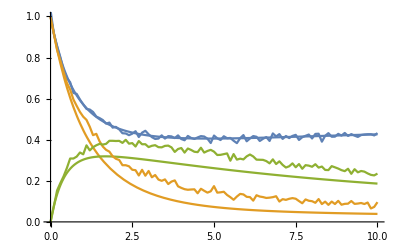

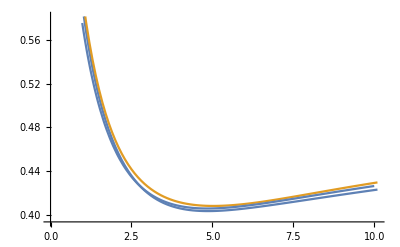

```mathematica
Clear[sol,model,fit]
sol=ParametricNDSolveValue[{
a'[t]==-k1 a[t] b[t]+k2 x[t],
a[0]==1,
b'[t]==-k1 a[t] b[t]+k2 x[t]-k3 b[t] x[t],
b[0]==1,
x'[t]==k1 a[t] b[t]-k2 x[t]-k3 b[t] x[t],
x[0]==0},
{a,b,x},
{t,0,10},
{k1,k2,k3}
]

model[k1_,k2_,k3_][i_,t_]:=Through[sol[k1,k2,k3][t],List][[i]]/;And@@NumericQ/@{k1,k2,k3,i,t};
model[0.85,0.15,0.5][2,10];
sol[0.85,0.15,0.5]

abscissae=Range[0.,10.,0.1];
ordinates=With[{k1=0.85,k2=0.15,k3=0.50},Through[sol[k1,k2,k3][abscissae],List]];
data=ordinates+RandomVariate[NormalDistribution[0,0.1^2],Dimensions[ordinates]];
transformedData={ConstantArray[Range@Length[ordinates],Length[abscissae]]//Transpose,ConstantArray[abscissae,Length[ordinates]],data}~Flatten~{{2,3},{1}};


fit=NonlinearModelFit[transformedData[[1;;101]],model[k1,k2,k3][i,t],{k1,k2,k3},{i,t}]; //Quiet
fit["BestFitParameters"];
Show[
Plot[{fit[1,t],fit[2,t],fit[3,t]},{t,0,10}],
ListLinePlot[data,DataRange->{0,10},PlotRange->All,AxesOrigin->{0,0}]
]
ciraw=fit["MeanPredictionConfidenceIntervals",ConfidenceLevel->.9];
Show[
ListPlot[{
MapIndexed[{First[#2]/10,#1[[1]]}&,ciraw[[;;101]]],
MapIndexed[{First[#2]/10,#1[[2]]}&,ciraw[[;;101]]]
},Joined->True,Filling->{2->{1}}],
Plot[fit[1,t],{t,0,10}]
]
```

```mathematica
daysUntilNotInfectiousOrHospitalized0=7.1;
```

```mathematica
fitCountry[country_]:=Module[{distancing, sol},
distancing[t_]:=Piecewise[countryHistoricalDistancing[country,t]];
params=countryParams[country,pC0,pH0,medianHospitalizationAge0,ageCriticalDependence0,ageHospitalizedDependence0];
sol=ParametricNDSolveValue[{
Sq'[t] ==(-distancing[t]* r0natural*Iq[t]*Sq[t])/daysUntilNotInfectiousOrHospitalized0- est[t]*Sq[t], (*Susceptible *)
Eq'[t] ==( distancing[t]* (* Exposed *)
		 r0natural*
		Iq[t]*
		Sq[t]) /daysUntilNotInfectiousOrHospitalized0
+ est[t]*Sq[t] 
- Eq[t]/daysFromInfectedToInfectious0,
Iq[t]==ISq[t] + IHq[t] + ICq[t] (* Infectious total, not yet PCR confirmed, age indep *),
ISq'[t] == pS0*Eq[t]/daysFromInfectedToInfectious0 - ISq[t]/daysUntilNotInfectiousOrHospitalized0, (* Infected without needing care *)
RSq'[t] == ISq[t]/daysUntilNotInfectiousOrHospitalized0, (* Recovered without needing care *)
IHq'[t] ==pH0*Eq[t]/daysFromInfectedToInfectious0 - IHq[t]/daysUntilNotInfectiousOrHospitalized0, (* Infected and will need hospital, won't need critical care *)
HHq'[t]== IHq[t]/daysUntilNotInfectiousOrHospitalized0 - HHq[t]/daysToLeaveHosptialNonCritical0, (* Going to hospital *) 
RHq'[t] == HHq[t]/daysToLeaveHosptialNonCritical0, (* Recovered after hospitalization *)
PCR'[t] == (pPCRNH0*Iq[t])/daysToGetTestedIfNotHospitalized0 + (pPCRH0*HHq[t])/daysToGetTestedIfHospitalized0, (* pcr confirmation *)
ICq'[t] == pC0*Eq[t]/daysFromInfectedToInfectious0 - ICq[t]/daysUntilNotInfectiousOrHospitalized0, (* Infected, will need critical care *)
HCq'[t] == ICq[t]/daysUntilNotInfectiousOrHospitalized0- HCq[t]/daysTogoToCriticalCare0, (* Hospitalized, need critical care *)
CCq'[t] ==HCq[t]/daysTogoToCriticalCare0 - CCq[t]/daysFromCriticalToRecoveredOrDeceased0 (* Entering critical care *),
Deaq'[t]==CCq[t]*If[CCq[t]>=icuCapacity,2*fractionOfCriticalDeceased0,fractionOfCriticalDeceased0]/daysFromCriticalToRecoveredOrDeceased0,
RCq'[t] == CCq[t]*(1-fractionOfCriticalDeceased0)/daysFromCriticalToRecoveredOrDeceased0(* Leaving critical care *),
est'[t] == 0,
WhenEvent[t>=importtime , est[t]->Exp[-initialInfectionImpulse0]], 
WhenEvent[t >importtime+importlength0, est[t]->0 ],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,Deaq[0]==0,est[0]==0,PCR[0]==0
},
{PCR,Deaq,Sq, Eq, ISq, RSq, IHq, HHq, RHq, Iq,ICq, HCq, CCq,est},
{t, 0, 300},
{r0natural,importtime}
];

model[
r0natural_,importtime_
][i_,t_]:=Through[sol[
r0natural,importtime
][t],List][[i]]/;And@@NumericQ/@{r0natural,importtime,i,t};

longData=Select[Join[{1,#["day"],(#["positive"]/params["Population"])//N}&/@countryData[country],
{2,#["day"],If[TrueQ[#["death"]==Null],0,(#["death"]/params["Population"])//N]}&/@countryData[country]],#[[3]]>0&];

fit=NonlinearModelFit[
longData,
model[r0natural,importtime][i,t],
{{r0natural, r0natural0},{importtime, params["importtime0"]}},
{i,t}];


Row[{
Text[country],
Show[
Plot[{fit[1,t]},{t,60,200}, PlotRange->{0,0.001}],
ListPlot[{
{#["day"],#["positive"]/params["Population"]}&/@countryData[country]
},PlotStyle->Black,PlotRange->{0,0.001}]
],
Show[
Plot[{fit[2,t]},{t,60,200}, PlotRange->{0,0.00001}],
ListPlot[{
{#["day"],#["death"]/params["Population"]}&/@countryData[country]
},PlotStyle->Black,PlotRange->{0,0.00001}]
],
fit["BestFitParameters"]
}
]
  
]
```

```mathematica
fitCountry[#]&/@countries
```

```mathematica
usParams=countryParams["United States",pC0,pH0,medianHospitalizationAge0,ageCriticalDependence0,ageHospitalizedDependence0];frParams=countryParams["France",pC0,pH0,medianHospitalizationAge0,ageCriticalDependence0,ageHospitalizedDependence0];
esParams=countryParams["Spain",pC0,pH0,medianHospitalizationAge0,ageCriticalDependence0,ageHospitalizedDependence0];
itParams=countryParams["Italy",pC0,pH0,medianHospitalizationAge0,ageCriticalDependence0,ageHospitalizedDependence0];
```

```mathematica
Clear[sol,model,fit]
sol=ParametricNDSolveValue[{
SqUS'[t]==(-Piecewise[countryHistoricalDistancing["United States",t]]*r0natural*IqUS[t]*SqUS[t])/daysUntilNotInfectiousOrHospitalized-estUS[t]*SqUS[t],(*Susceptible*)EqUS'[t]==(Piecewise[countryHistoricalDistancing["United States",t]]*(*Exposed*)r0natural*IqUS[t]*SqUS[t])/daysUntilNotInfectiousOrHospitalized
+estUS[t]*SqUS[t]
-EqUS[t]/daysFromInfectedToInfectious,IqUS[t]==ISqUS[t]+IHqUS[t]+ICqUS[t] (*Infectious total,not yet PCR confirmed,age indep*),ISqUS'[t]==pS0*EqUS[t]/daysFromInfectedToInfectious-ISqUS[t]/daysUntilNotInfectiousOrHospitalized,(*Infected without needing care*)RSqUS'[t]==ISqUS[t]/daysUntilNotInfectiousOrHospitalized,(*Recovered without needing care*)IHqUS'[t]==pH0*EqUS[t]/daysFromInfectedToInfectious0-IHqUS[t]/daysUntilNotInfectiousOrHospitalized,(*Infected and will need hospital,won't need critical care*)HHqUS'[t]==IHqUS[t]/daysUntilNotInfectiousOrHospitalized-HHqUS[t]/daysToLeaveHosptialNonCritical0,(*Going to hospital*)RHqUS'[t]==HHqUS[t]/daysToLeaveHosptialNonCritical0,(*Recovered after hospitalization*)PCRUS'[t]==(pPCRNH0*IqUS[t])/daysToGetTestedIfNotHospitalized0+(pPCRH0*HHqUS[t])/daysToGetTestedIfHospitalized0,(*pcr confirmation*)ICqUS'[t]==pC0*EqUS[t]/daysFromInfectedToInfectious-ICqUS[t]/daysUntilNotInfectiousOrHospitalized,(*Infected,will need critical care*)HCqUS'[t]==ICqUS[t]/daysUntilNotInfectiousOrHospitalized-HCqUS[t]/daysTogoToCriticalCare0,(*Hospitalized,need critical care*)CCqUS'[t]==HCqUS[t]/daysTogoToCriticalCare0-CCqUS[t]/daysFromCriticalToRecoveredOrDeceased0 (*Entering critical care*),DeaqUS'[t]==CCqUS[t]*If[CCqUS[t]≥icuCapacity,2*fractionOfCriticalDeceased0,fractionOfCriticalDeceased0]/daysFromCriticalToRecoveredOrDeceased0,RCqUS'[t]==CCqUS[t]*(1-fractionOfCriticalDeceased0)/daysFromCriticalToRecoveredOrDeceased0(*Leaving critical care*),estUS'[t]==0,WhenEvent[t≥usParams["importtime0"],estUS[t]->Exp[-initialInfectionImpulse0]],WhenEvent[t>usParams["importtime0"]+importlength0,estUS[t]->0],SqUS[0]==1,EqUS[0]==0,ISqUS[0]==0,RSqUS[0]==0,IHqUS[0]==0,HHqUS[0]==0,RHqUS[0]==0,ICqUS[0]==0,HCqUS[0]==0,CCqUS[0]==0,RCqUS[0]==0,DeaqUS[0]==0,estUS[0]==0,PCRUS[0]==0,SqFR'[t]==(-Piecewise[countryHistoricalDistancing["France",t]]*r0natural*IqFR[t]*SqFR[t])/daysUntilNotInfectiousOrHospitalized-estFR[t]*SqFR[t],(*Susceptible*)EqFR'[t]==(Piecewise[countryHistoricalDistancing["France",t]]*(*Exposed*)r0natural*IqFR[t]*SqFR[t])/daysUntilNotInfectiousOrHospitalized
+estFR[t]*SqFR[t]
-EqFR[t]/daysFromInfectedToInfectious,IqFR[t]==ISqFR[t]+IHqFR[t]+ICqFR[t] (*Infectious total,not yet PCR confirmed,age indep*),ISqFR'[t]==pS0*EqFR[t]/daysFromInfectedToInfectious0-ISqFR[t]/daysUntilNotInfectiousOrHospitalized,(*Infected without needing care*)RSqFR'[t]==ISqFR[t]/daysUntilNotInfectiousOrHospitalized,(*Recovered without needing care*)IHqFR'[t]==pH0*EqFR[t]/daysFromInfectedToInfectious-IHqFR[t]/daysUntilNotInfectiousOrHospitalized,(*Infected and will need hospital,won't need critical care*)HHqFR'[t]==IHqFR[t]/daysUntilNotInfectiousOrHospitalized-HHqFR[t]/daysToLeaveHosptialNonCritical0,(*Going to hospital*)RHqFR'[t]==HHqFR[t]/daysToLeaveHosptialNonCritical0,(*Recovered after hospitalization*)PCRFR'[t]==(pPCRNH0*IqFR[t])/daysToGetTestedIfNotHospitalized0+(pPCRH0*HHqFR[t])/daysToGetTestedIfHospitalized0,(*pcr confirmation*)ICqFR'[t]==pC0*EqFR[t]/daysFromInfectedToInfectious-ICqFR[t]/daysUntilNotInfectiousOrHospitalized,(*Infected,will need critical care*)HCqFR'[t]==ICqFR[t]/daysUntilNotInfectiousOrHospitalized-HCqFR[t]/daysTogoToCriticalCare0,(*Hospitalized,need critical care*)CCqFR'[t]==HCqFR[t]/daysTogoToCriticalCare0-CCqFR[t]/daysFromCriticalToRecoveredOrDeceased0 (*Entering critical care*),DeaqFR'[t]==CCqFR[t]*If[CCqFR[t]≥icuCapacity,2*fractionOfCriticalDeceased0,fractionOfCriticalDeceased0]/daysFromCriticalToRecoveredOrDeceased0,RCqFR'[t]==CCqFR[t]*(1-fractionOfCriticalDeceased0)/daysFromCriticalToRecoveredOrDeceased0(*Leaving critical care*),estFR'[t]==0,WhenEvent[t≥frParams["importtime0"],estFR[t]->Exp[-initialInfectionImpulse0]],WhenEvent[t>frParams["importtime0"]+importlength0,estFR[t]->0],SqFR[0]==1,EqFR[0]==0,ISqFR[0]==0,RSqFR[0]==0,IHqFR[0]==0,HHqFR[0]==0,RHqFR[0]==0,ICqFR[0]==0,HCqFR[0]==0,CCqFR[0]==0,RCqFR[0]==0,DeaqFR[0]==0,estFR[0]==0,PCRFR[0]==0
},
{PCRUS,DeaqUS,PCRFR,DeaqFR,
SqUS,EqUS,ISqUS,RSqUS,IHqUS,HHqUS,RHqUS,IqUS,ICqUS,HCqUS,CCqUS,estUS,SqFR,EqFR,ISqFR,RSqFR,IHqFR,HHqFR,RHqFR,IqFR,ICqFR,HCqFR,CCqFR,estFR},
{t, 0, 300},
{r0natural,daysUntilNotInfectiousOrHospitalized,daysFromInfectedToInfectious}
];

model[
r0natural_,daysUntilNotInfectiousOrHospitalized_,daysFromInfectedToInfectious_
][i_,t_]:=Through[sol[
r0natural,daysUntilNotInfectiousOrHospitalized, daysFromInfectedToInfectious
][t],List][[i]]/;And@@NumericQ/@{r0natural,daysUntilNotInfectiousOrHospitalized,daysFromInfectedToInfectious,i,t};
```

```mathematica
sol
```

ParametricFunction[<>]

```mathematica
model[r0natural0,daysUntilNotInfectiousOrHospitalized0,daysFromInfectedToInfectious0][3,85]
```

0.0215873

```mathematica
longData=Select[Join[
{1,#["day"],(#["positive"]/params["Population"])//N}&/@countryData["United States"],
{2,#["day"],If[TrueQ[#["death"]==Null],0,(#["death"]/usParams["Population"])//N]}&/@countryData["United States"],
{3,#["day"],(#["positive"]/params["Population"])//N}&/@countryData["France"],
{4,#["day"],If[TrueQ[#["death"]==Null],0,(#["death"]/frParams["Population"])//N]}&/@countryData["France"]
]
,#[[3]]>0&];
```

```mathematica
fit=NonlinearModelFit[
longData,
{
model[r0natural,daysUntilNotInfectiousOrHospitalized,daysFromInfectedToInfectious][i,t],
r0natural≥ 2.5,
daysUntilNotInfectiousOrHospitalized≥2,
daysFromInfectedToInfectious0≥2
},
{{r0natural, 4.79525254406081},{daysUntilNotInfectiousOrHospitalized,3.1307011233683464},{daysFromInfectedToInfectious,2.114075243719123}},
{i,t},
PrecisionGoal->4,
PrecisionGoal->4,
EvaluationMonitor:>Print["r0natural=",r0natural,".    daysUntilNotInfectiousOrHospitalized=",daysUntilNotInfectiousOrHospitalized,".    daysFromInfectedToInfectious=",daysFromInfectedToInfectious]];
```